```mathematica
GCD[1000,26]
```

2

```mathematica
Clear[gg,pp]
gg[n_,d_,k_] := gg[n,d,k]=Sum[ GCD[j,d](1/k- gg[Floor[n/j],d,k+1]),{j,2,n}]
pp[n_,k_] :=pp[n,k]= Sum[1/k-pp[Floor[n/j],k+1],{j,2,n}]
```

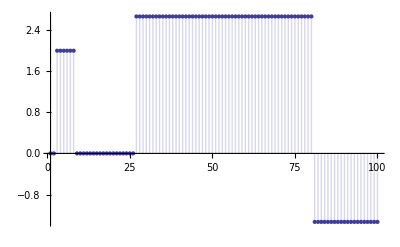

```mathematica
DiscretePlot[gg[n,3,1]-pp[n,1],{n,1,100}]
```

```mathematica
Table[gg[n,3,1]-pp[n,1],{n,1,100}]
```

{0,0,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,8/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3,-4/3}

```mathematica
Sum[ GCD[j,k],{j,1,100},{k,1,100/j}]
```

725

```mathematica
Clear[g1]
g1[n_,k_] := g1[n,k]=Sum[ GCD[a,b]g1[Floor[n/(a b)],k-1],{a,1,n},{b,1,n/a}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) Binomial[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 2pr[n,0]+pr[n^(1/2),1]-pr[n^(1/2),0]
```

```mathematica
Table[{n, lg[2^n]-lg[2^n-1], lg[3^n]-lg[3^n-1], lg[5^n]-lg[5^n-1], lg[7^n]-lg[7^n-1]},{n,1,6}]//TableForm
```

$Aborted

```mathematica
Table[{2^n, lg[2^n]-lg[2^n-1]-2kk[2^n]},{n,1,10}]//TableForm
```

2 | 0
4 | 1
8 | 0
16 | 3/2
32 | 0
64 | 7/3
128 | 0
256 | 15/4
512 | 0
1024 | 31/5

```mathematica
Table[{3^n, lg[3^n]-lg[3^n-1]-2kk[2^n]},{n,1,7}]//TableForm
```

3 | 0
9 | 2
27 | 0
81 | 4
243 | 0
729 | 26/3
2187 | 0

```mathematica
Table[{5^n, lg[5^n]-lg[5^n-1]},{n,1,6}]//TableForm
```

5 | 2
25 | 5
125 | 2/3
625 | 25/2
3125 | 2/5
15625 | 125/3

```mathematica
Table[{7^n, lg[7^n]-lg[7^n-1]},{n,1,4}]//TableForm
```

7 | 2
49 | 7
343 | 2/3
2401 | 49/2

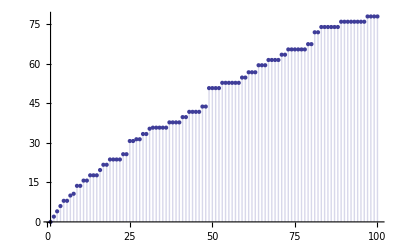

```mathematica
DiscretePlot[ts[n],{n,1,100}]
```

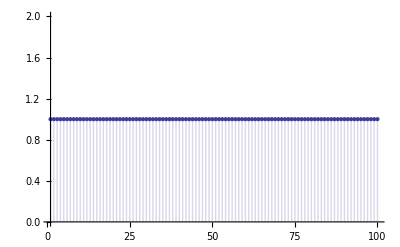

```mathematica
DiscretePlot[lg[n]-ts[n]+1,{n,1,100}]
```

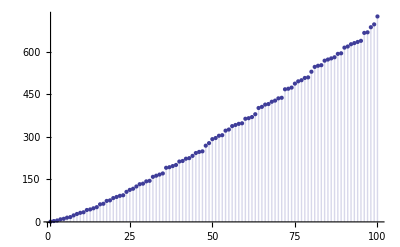

```mathematica
DiscretePlot[ g1[n,1],{n,1,100}]
```

```mathematica
gh[n_] := Sum[ 1 1 l MoebiusMu[m],{j,1,n},{k,1,n/j},{l,1,(n/( j k))^(1/2)},{m,1,(n/(j k l^2))^(1/2)}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=dz[n,z]=Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}]
gh2[n_] := Sum[ dz[j,2] l MoebiusMu[m],{j,1,n},{l,1,(n/( j))^(1/2)},{m,1,(n/(j l^2))^(1/2)}]
gh3[n_] := Sum[ Abs[MoebiusMu[j]] l ,{j,1,n},{k,1,n/j},{l,1,(n/( j k))^(1/2)}]
gh4[n_] := Sum[ dz[j,2]EulerPhi[l] ,{j,1,n},{l,1,(n/( j))^(1/2)}]
gh5[n_] := Sum[ dz[j,2]EulerPhi[l] ,{l,1,n^(1/2)},{j,1,n/l^2}]
```

```mathematica
DiscretePlot[ gh4[n],{n,1,100}]
```

-Graphics-

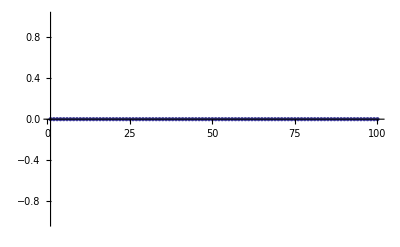

```mathematica
DiscretePlot[g1[n,1]- gh[n],{n,1,100}]
```

```mathematica
Clear[g1]
g1[n_,k_] := g1[n,k]=Sum[ GCD[a,b,c]g1[Floor[n/(a b c)],k-1],{a,1,n},{b,1,n/a}, {c,1,n/(a b)}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) Binomial[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 3pr[n,0]+pr[n^(1/3),1]-pr[n^(1/3),0]
```

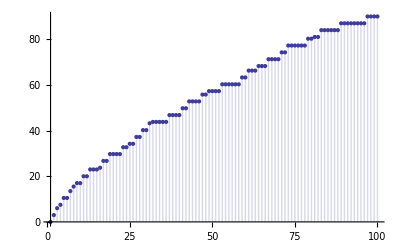

```mathematica
DiscretePlot[ lg[n],{n,1,100}]
```

```mathematica
DiscretePlot[lg[n]-ts[n],{n,1,100}]
```

-Graphics-

```mathematica
Clear[g1]
g1[n_,k_] := g1[n,k]=Sum[ GCD[a,b,c,d]g1[Floor[n/(a b c d)],k-1],{a,1,n},{b,1,n/a}, {c,1,n/(a b)}, {d,1,n/(a b c)}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) Binomial[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 4pr[n,0]+pr[n^(1/4),1]-pr[n^(1/4),0]
```

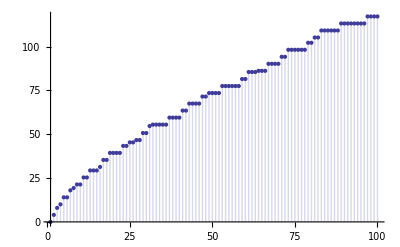

```mathematica
DiscretePlot[ lg[n],{n,1,100}]
```

```mathematica
DiscretePlot[ lg[n]-ts[n],{n,1,100}]
```

-Graphics-

```mathematica
gg[n_]:=Sum[ GCD[j,n],{j,1,n}]
gb[n_] := Sum[ gg[j],{j,1,n}]
ga[n_] := Sum[ j k MoebiusMu[l],{j,1,n},{k,1,n/j}, {l,1,n/(j k)}]
gc[n_] := Sum[ j EulerPhi[k],{j,1,n},{k,1,n/j}]
```

```mathematica
gb[100]
```

18065

```mathematica
ga[100]
```

18065

```mathematica
gc[100]
```

18065